```mathematica
mP=1.67*10^(-24); (*g*)
kB=1.38*10^(-16); (*in cgs*)
G=6.67*10^(-8);   (*in cgs*)
h=6.63*10^(-27); (*in cgs*)
Msun=1.989*10^33;
Rsun=6.9598*10^10;
Lsun=3.8418*10^33;
c=3*10^10;   (*cm/s*)
sigmaSB=5.67*10^(-5); 
a=4*sigmaSB/c;   
γ=5/3 ;
mu=0.62;
```

```mathematica
Polinomi=Table[q^i,{i,0,10}];
```

```mathematica
SolarModel0=Import["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\SolarRotation\\BalbusEquation\\SolarModelBS2005-AGS,OP","Table"];

SolarModel=Drop[SolarModel0,1];
SolarModel=Drop[SolarModel,-3];

RadiusMass=Table[{ Rsun*SolarModel[[All,2]][[i]],Msun*SolarModel[[All,1]][[i]]},{i,1,Dimensions[SolarModel][[1]]}];
RadiusTemp=Table[{Rsun*SolarModel[[All,2]][[i]],SolarModel[[All,3]][[i]]},{i,1,Dimensions[SolarModel][[1]]}];
RadiusDens=Table[{Rsun*SolarModel[[All,2]][[i]],SolarModel[[All,4]][[i]]},{i,1,Dimensions[SolarModel][[1]]}];
RadiusPress=Table[{Rsun*SolarModel[[All,2]][[i]],SolarModel[[All,5]][[i]]},{i,1,Dimensions[SolarModel][[1]]}];
RadiusLumin=Table[{Rsun*SolarModel[[All,2]][[i]],Lsun*SolarModel[[All,6]][[i]]},{i,1,Dimensions[SolarModel][[1]]}];
RadiusFlux=Table[{Rsun*SolarModel[[All,2]][[i]],Lsun*SolarModel[[All,6]][[i]]/(4*Pi*(RadiusTemp[[i]][[1]])^2)},{i,1,Dimensions[SolarModel][[1]]}];
RadiusGrav=Table[{RadiusMass[[i]][[1]],G*RadiusMass[[i]][[2]]/(RadiusMass[[i]][[1]])^2},{i,1,Dimensions[RadiusMass][[1]]}];
```

```mathematica
RhoN=Interpolation[RadiusDens];
PN=Interpolation[RadiusPress];
TN=Interpolation[RadiusTemp];
Grav=Interpolation[RadiusGrav];

RDown=Rsun*0.1;
RUp=Rsun*0.9;
```

```mathematica
RadiusGravReduced=Select[RadiusGrav,RDown<#[[1]]<RUp&];
RadiusTempReduced=Select[RadiusTemp,RDown<#[[1]]<RUp&];
RadiusPressReduced=Select[RadiusPress,RDown<#[[1]]<RUp&];
RadiusDensReduced=Select[RadiusDens,RDown<#[[1]]<RUp&];
```

```mathematica
RhoFit0=Fit[RadiusDensReduced,Polinomi,q];
RhoFit[x_]=RhoFit0/.{q->x};
Show[Plot[RhoN[r],{r,RDown,RUp}],ListPlot[RadiusDensReduced],Plot[RhoFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","rho (g/cm^3)","Density"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
ρ[R_,z_]=RhoFit[(R^2+z^2)^0.5];
```

```mathematica
TempFit0=Fit[RadiusTempReduced,Polinomi,q];
TempFit[x_]=TempFit0/.{q->x};
Show[Plot[TN[r],{r,RDown,RUp}],ListPlot[RadiusTempReduced],Plot[TempFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","T (K)","Temperature"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
T[R_,z_]=TempFit[(R^2+z^2)^0.5];
```

```mathematica
PressFit0=Fit[RadiusPressReduced,Polinomi,q];
PressFit[x_]=PressFit0/.{q->x};
Show[Plot[PN[r],{r,RDown,RUp}],ListPlot[RadiusPressReduced],Plot[PressFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","P (g/(cm*s^2))","Pressure"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
P[R_,z_]=PressFit[(R^2+z^2)^0.5];
PdR[R_,z_]=D[P[R,z],R];   Pdz[R_,z_]=D[P[R,z],z];
dLogPdLogr[R_,z_]=(P[R,z]/(√(R^2+z^2)))^-1*PressFit'[√(R^2+z^2)];
```

```mathematica
Om0SqList=Import["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\AngularMomentumTransfer\\Minimum Pr\\Omega0SqGONG.dat"];
Om0SqFit0=Fit[Om0SqList,Polinomi,q];
Om0SqFit[x_]=Om0SqFit0/.{q->(x/Rsun)};
Show[Plot[Om0SqFit[r],{r,0.5Rsun,0.72Rsun}],ListPlot[Om0SqList,PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","Omega0Sq (rad/s^2)"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
Om2SqList=Import["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\AngularMomentumTransfer\\Minimum Pr\\Omega2SqGONG.dat"];
Om2SqFit0=Fit[Om2SqList,Polinomi,q];
Om2SqFit[x_]=Om2SqFit0/.{q->(x/Rsun)};
Show[Plot[Om2SqFit[r],{r,0.5Rsun,0.72Rsun}],ListPlot[Om2SqList,PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","Omega2Sq (rad/s^2)"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
```

```mathematica
OmegaFit[r_,θ_]=√(Om0SqFit[r]+Om2SqFit[r]*Cos[θ]^2);
ΩSqdr[r_,θ_]:=(Om0SqFit[r+5*10^5]-Om0SqFit[r-5*10^5])/(10*10^5)+(Om2SqFit[(r+5*10^5)]-Om2SqFit[r-5*10^5])/(10*10^5)*Cos[θ]^2
ΩSqdθ[r_,θ_]:=-2*Sin[θ]*Cos[θ]*Om2SqFit[r]

Ω[R_,z_]:=OmegaFit[((R^2+z^2)^0.5),ArcTan[R/z]];
ΩdR[R_,z_]:=1/(2Ω[R,z])(R/(√(R^2+z^2))ΩSqdr[√(R^2+z^2),ArcTan[R/z]]+z/(R^2+z^2)*ΩSqdθ[√(R^2+z^2),ArcTan[R/z]])
Ωdz[R_,z_]:=1/(2Ω[R,z])(z/(√(R^2+z^2))ΩSqdr[√(R^2+z^2),ArcTan[R/z]]-R/(R^2+z^2)*ΩSqdθ[√(R^2+z^2),ArcTan[R/z]])
ΩRdR[R_,z_]:=ΩdR[R,z]*R+Ω[R,z]
ΩRdz[R_,z_]:=Ωdz[R,z]*R
```

```mathematica
dLogΩdLogR[R_,z_]:=(R/Ω[R,z])*ΩdR[R,z]
dLogΩdLogz[R_,z_]:=(z/Ω[R,z])*Ωdz[R,z]
```

```mathematica
(* THESE APPLY IN THE RADIATIVE ZONE *)

σ[R_,z_]=Log[P[R,z]*ρ[R,z]^(-γ)];
σdR[R_,z_]=D[σ[R,z],R];
σdz[R_,z_]=D[σ[R,z],z];
σdr[R_,z_]=σdR[R,z]*R/(√(R^2+z^2))+σdz[R,z]*z/(√(R^2+z^2));
σdLogr[R_,z_]=√(R^2+z^2)*σdr[R,z];
```

```mathematica
(* THESE APPLY IN THE CONVECTIVE ZONE

dσdLogr=-2.3*10^-5;
dσdθ=(rper*γ*Rper)/Grav[rper]*2*Ω[Rper,zper]*Ωdz[Rper,zper]; (*Balbus says it is -4*10^-6*)
σdR[R_,z_]=Sin[θper]*1/rper*dσdLogr+Cos[θper]*1/rper dσdθ*1

σdz[R_,z_]=Cos[θper]*1/rper*dσdLogr-Sin[θper]*1/rper*dσdθ*1    *)
(*σdz[R_,z_]=Pdz[Rper,zper]/PdR[Rper,zper] σdR[R,z]*)
```

```mathematica
AngMom[R_,z_]:=(Ω[R,z] R^2);

ldR:=(AngMom[Rper+10^4,zper]-AngMom[Rper,zper])/10^4;
ldz:=(AngMom[Rper,zper+10^4]-AngMom[Rper,zper])/10^4;

l2dR:=(AngMom[Rper+10^4,zper]^2-AngMom[Rper,zper]^2)/10^4;
l2dz:=(AngMom[Rper,zper+10^4]^2-AngMom[Rper,zper]^2)/10^4;

Ω2dR:=(Ω[Rper+10^4,zper]^2-Ω[Rper,zper]^2)/10^4;
Ω2dz:=(Ω[Rper,zper+10^4]^2-Ω[Rper,zper]^2)/10^4;
```

```mathematica
BR[R_,z_]=0;
Bϕ[R_,z_]=0;
Bz[R_,z_]=0;


UaR[R_,z_]=0;
Uaϕ[R_,z_]=0;
Uaz[R_,z_]=0;
```

```mathematica
(Ω[0.6Rsun*Sin[π/4],0.6Rsun*Cos[π/4]]*0.6Rsun)^2/(γ*P[0.6Rsun*Sin[π/4],0.6Rsun*Cos[π/4]]/ρ[0.6Rsun*Sin[π/4],0.6Rsun*Cos[π/4]])
dLogPdLogr[0.6Rsun*Sin[π/4],0.6Rsun*Cos[π/4]]
σdLogr[0.6Rsun*Sin[π/4],0.6Rsun*Cos[π/4]]
dLogΩdLogR[0.6Rsun*Sin[π/4],0.6Rsun*Cos[π/4]]
dLogΩdLogz[0.6Rsun*Sin[π/4],0.6Rsun*Cos[π/4]]
(Ω[0.7Rsun*Sin[π/4],0.7Rsun*Cos[π/4]]*0.7Rsun)^2/(γ*P[0.7Rsun*Sin[π/4],0.7Rsun*Cos[π/4]]/ρ[0.7Rsun*Sin[π/4],0.7Rsun*Cos[π/4]])
dLogPdLogr[0.7Rsun*Sin[π/4],0.7Rsun*Cos[π/4]]
σdLogr[0.7Rsun*Sin[π/4],0.7Rsun*Cos[π/4]]
dLogΩdLogR[0.7Rsun*Sin[π/4],0.7Rsun*Cos[π/4]]
dLogΩdLogz[0.7Rsun*Sin[π/4],0.7Rsun*Cos[π/4]]
```

0.000017868

-6.92968

2.61737

-0.00108207

-0.019819

0.0000324788

-9.10286

1.14509

-0.113427

-0.240187

```mathematica
Num[x_,R_,z_]=-(2γ)/(-(dLogPdLogr[R,z]*σdLogr[R,z]))*(2+dLogΩdLogR[R,z]-x*(R/z)*dLogΩdLogz[R,z])/((x*z/(√(R^2+z^2))-R/(√(R^2+z^2)))^2);
```

```mathematica
NumFactTable=Table[{θ,r/Rsun,NMaximize[{Num[x,r*Sin[θ],r*Cos[θ]],x>-10^6,x<10^6},x][[1]]},{θ,5/180 Pi,85/180 Pi,5/180 Pi},{r,0.5Rsun,0.7Rsun,0.002Rsun}]
(*Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\AngularMomentumTransfer\\Minimum Pr\\NumFactData.dat",NumFactTable,"Table"]
NumFactTable=Import["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\AngularMomentumTransfer\\Minimum Pr\\NumFactData.dat","Table"]*)
```

{{{π/36,0.5,8.70903×10^-10},{π/36,0.502,3.12803×10^-9},{π/36,0.504,1.63587×10^-8},{π/36,0.506,3.3356×10^-8},94,{π/36,0.696,0.000489412},{π/36,0.698,0.000516228},{π/36,0.7,0.00053898}},15,{1}}
 |  |  |  |

```mathematica
NumFactFunction=Interpolation[Flatten[NumFactTable,1]];
```

```mathematica
NumPlot15=Plot[NumFactFunction[15Pi/180,x],{x,0.5,0.7},PlotRange->{{0.5,0.7},{0,0.005}},PlotStyle->Directive[Black,Dashed],Frame->True];
NumPlot45=Plot[NumFactFunction[45Pi/180,x],{x,0.5,0.7},PlotRange->{{0.5,0.7},{0,0.005}},PlotStyle->Directive[Black]];
NumPlot75=Plot[NumFactFunction[75Pi/180,x],{x,0.5,0.7},PlotRange->{{0.5,0.7},{0,0.005}},PlotStyle->Directive[Black,Dotted]];
Show[NumPlot15,NumPlot45,NumPlot75,FrameLabel->{"r / R_⊙","Max[N(x;r,θ)]"},BaseStyle->{FontWeight->"Plain",FontSize->16},LabelStyle->Black,FrameStyle->Black,BaseStyle->{FontWeight->"Plain",FontSize->12}]
```

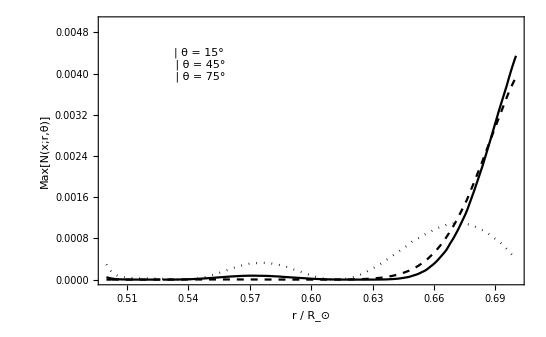

```mathematica
LegendKey={{"θ = 15°",Black,Dashed},{"θ = 45°",Black, None},{"θ = 75°", Black, Dotted}};
CaptionGeneral[LegendKey];
```

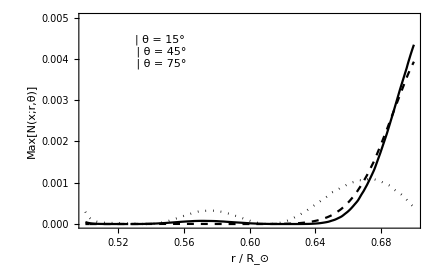
```mathematica
NumFactPlot=-Graphics-;

(*Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\AngularMomentumTransfer\\Minimum Pr\\picNumFact.png",NumFactPlot,ImageResolution->150]*)
```